## Lesson

Apply pure function to single item:

```mathematica
f[#,a]&[x]
```

f[x,a]

Apply pure function over list:

```mathematica
f[#,a]&/@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

## Questions

Q1. Use Range and a pure function to create a list of the first 20 squares.

```mathematica
#^2&[Range[20]]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

Q2. Make a list of the result of blending yellow, green and blue with red.

```mathematica
Blend[{Red,#}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

Q3. Generate a list of framed columns containing the uppercase and lowercase versions of each letter of the alphabet.

```mathematica
Framed[Column[{#,ToUpperCase[#]}]]&/@Alphabet[]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

Q4. Make a list of letters of the alphabet, in random colors, with frames having random background colors.

```mathematica
Style[Framed[Style[#,RandomColor[]]],RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Q5. Make a table of G5 countries, together with their flags, and arrange the result in a fully framed grid.






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
Grid[{#,#["Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]],Frame->All]
```

Q6. Make a list of word clouds for the Wikipedia articles about apple, peach and pear.

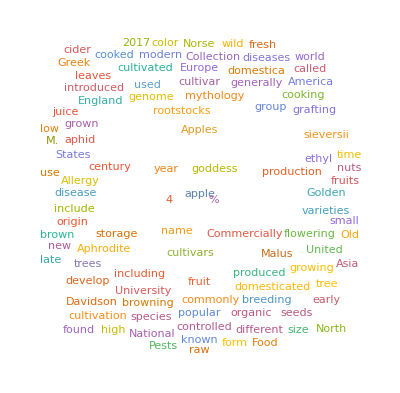
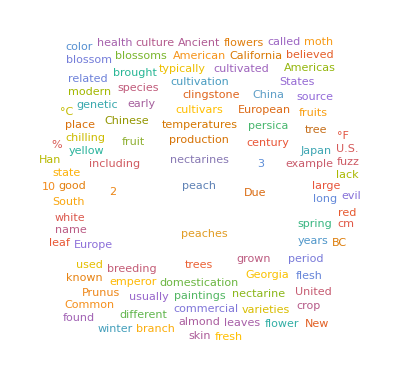
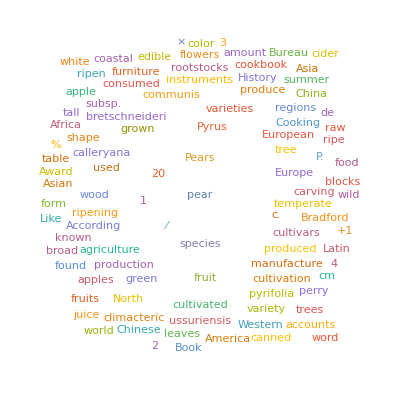

```mathematica
WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

Q7. Make a list of histograms of the word lengths in Wikipedia articles on apple, peach and pear.

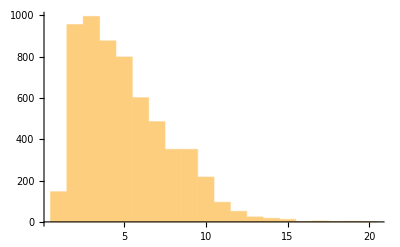
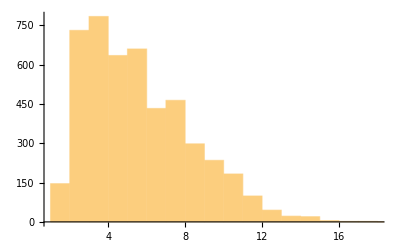
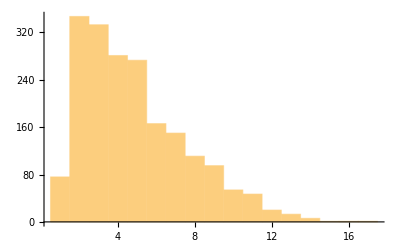

```mathematica
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

Q8. Make a list of maps of Central America, highlighting each country in turn.

```mathematica
GeoListPlot[{#},GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Extended Questions

+Q1. Give a simpler form for (#^2+1&)/@Range[10].

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}